## Eli — PS 5 — 2025-02-04

## EIWL3 Sections 14 and 17

## Chapter 14

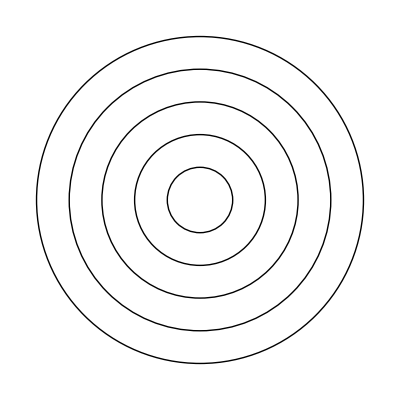

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,5}]]
```

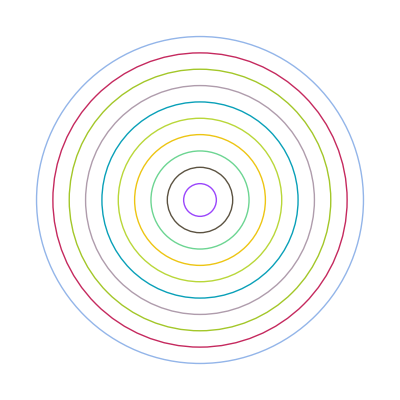

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,1,10}]]
```

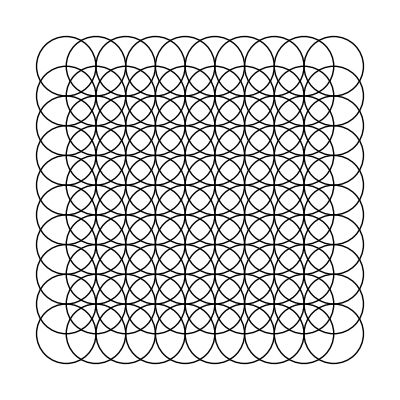

```mathematica
Graphics[Table[Circle[{x,y},1],{x,1,10},{y,1,10}]]
```

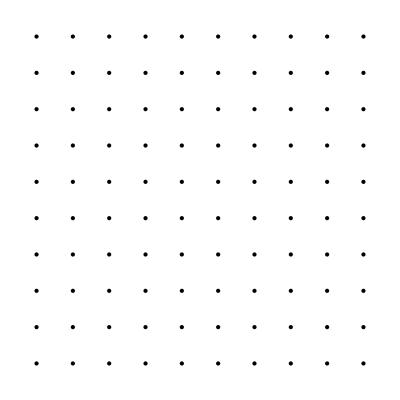

```mathematica
Graphics[Table[Point[{x,y}],{x,1,10},{y,1,10}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,1,n}]],{n,1,20,1}]
```

```mathematica
Graphics3D[Table[Style[Sphere[{RandomInteger[10,3]},1],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Show[%827,Axes->True,AxesStyle->Black]
```

Show::gtype: Out is not a type of graphics.

Show[%827,Axes→True,AxesStyle→GrayLevel[0]]

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z}],Hue[n]],{x,1,22,2},{y,1,22,2},{z,1,22,2},{n,0,1}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[Table[Circle[{t x,0},x],{x,1,10}]],{t,-2,2}]
```

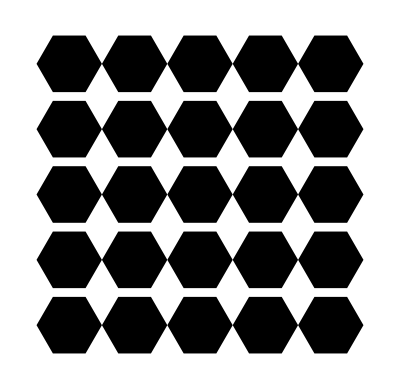

```mathematica
Graphics[Table[RegularPolygon[{x,y},0.5,6],{x,1,5},{y,1,5}]]
```

```mathematica
Graphics3D[Line[Table[RandomInteger[50,3],50]]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Style[{Icosahedron[{0,0,0},s],Dodecahedron[{0,0},1]},Opacity[0.5]]],{s,1,2}]
```

## Chapter 17

```mathematica
UnitConvert[,"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[, "Kilometers/hour"]
```

96.963 km/h

```mathematica
UnitConvert[["Height"],"Miles"]
```

0.205052 mi

```mathematica
["Elevation"]/["Height"]
```

26.8147

```mathematica
["Mass"]/["Mass"]
```

81.3

```mathematica
CurrencyConvert[Quantity[2500., "Yen"],]
```

16.44 $

```mathematica
UnitConvert[Plus[,,,],]
```

305.353 kg

```mathematica
UnitConvert[{["DistanceFromEarth"],["DistanceFromEarth"],["DistanceFromEarth"],["DistanceFromEarth"],["DistanceFromEarth"],["DistanceFromEarth"],["DistanceFromEarth"]},]
```

{6.19673 light minutes,3.66411 light minutes,11.4198 light minutes,39.2366 light minutes,87.3811 light minutes,162.484 light minutes,255.37 light minutes}

```mathematica
Rotate["hello",180 Degree]
```

hello

```mathematica
Table[Rotate["A",x Degree],{x,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate[["Image"],x Degree],{x,0,180}]
```

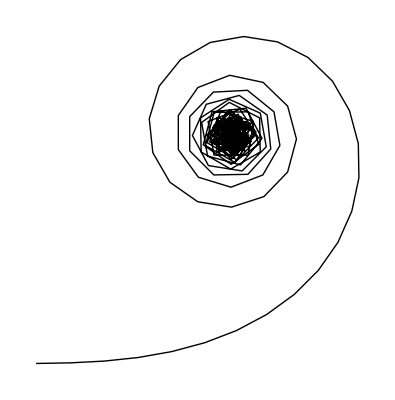

```mathematica
Graphics[Line[AnglePath[Range[180 ]Degree]]]
```

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[theta,100]]]],{theta,0,360}]
```

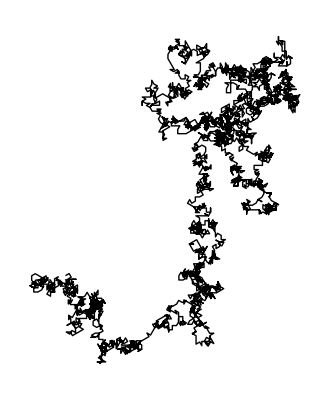

```mathematica
Graphics[Line[AnglePath[IntegerDigits[2^10000 ]30 Degree]]]
```